## QCD Parameters

### Running Coupling

From [1], we use the one-loop, MS-bar running coupling corresponding to four active flavors.  We take as our boundary condition α_s[M_τ]=0.326.

In the definition of α_s given, μ is in GeV.

```mathematica
Clear[α]
α[μ_]=Module[{Mτ=1.77686,ατ=0.326,nf=4,b0},
b0=1/(12π)(33-2nf);
ατ/(1+b0 ατ Log[μ^2/Mτ^2])
];
```

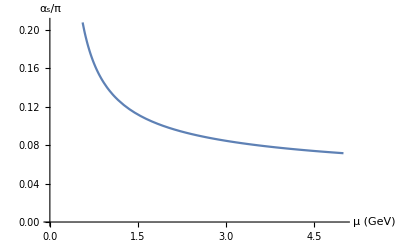

```mathematica
Plot[α[μ]/π,{μ,0.3,5},AxesOrigin->{0,0},AxesLabel->{"μ (GeV)","α_s/π"}]
```

### Running Quark Masses

From[1], we use the one-loop, MS-bar running light and strange quark masses.

Below, μ is in GeV.

```mathematica
mq[μ_]=Module[{mqat2=0.0035},
mqat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
ms[μ_]=Module[{msat2=0.095},
msat2(α[μ]/α[2])^(12/25)
];
```

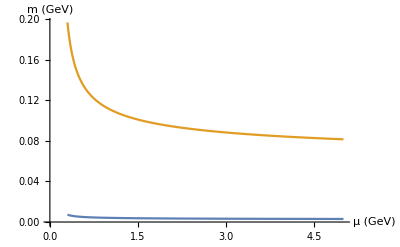

```mathematica
Plot[{mq[μ],ms[μ]},{μ,0.3,5},AxesOrigin->{0,0},AxesLabel->{"μ (GeV)","m (GeV)"}]
```

### Condensates

All given numerical values are in appropriate powers of GeV.

We use PCAC relations for the 4d light and strange quark condensates:

⟨m_q q̄ q⟩=-1/2 f_π^2 m_π^2

⟨m_s s̄ s⟩=-1/2 f_K^2 m_K^2.

Meson masses are taken from [1].  The pion decay constant is from [2].  The kaon decay constant is from....

```mathematica
mqq=-0.5 Mpi^2 fpi^2/.{Mpi->0.13957018,fpi->0.1304/(√2.)}
mss=-0.5 MK^2 fK^2/.{MK->0.493677,fK->0.1562/(√2.)}
```

-0.0000828096

-0.00148658

The 4d gluon condensate value is taken from [2]:

```mathematica
αGG=0.07(0.9);
```

Let κ be the strange quark condensate scaling ratio defined by

κ=(<s̄ s>)/(<d̄ d>).

From [2], we have that

```mathematica
κ=0.74;
```

For the mixed condensate, from [2,3]

```mathematica
M0=√0.8
```

0.894427

```mathematica
gqGq=2 M0^2 qq
gsGs=2 M0^2 ss
```

1.6 qq

1.6 ss

It looks as if there are improvements to be made to our implementation of the mixed condensate (see [2]).

For the 6d gluon condensate, we have from [2]:

```mathematica
gggGGG=(8.2) αGG(0)
```

0.

The following values of the 6d quark condensate come from [3] where deviations from the vacuum saturation hypothesis are taken into account:

```mathematica
(*αqqqq=1.3 10^-4*) (* exact vacuum saturation *)
αqqqq=1.8 10^-4
αssss=κ^2 αqqqq
```

0.00035

0.00019166

### References

[1] Olive et al. (Particle Data Group), Chin.Phys.C38, (2014) 090001

[2] Narison, Nuclear and Particle Physics Proceedings 00 (2015) 1 [arXiv:1511.05903v3]

[3] Latorre, Pascual, Narison, Z.Phys.C34 (1987) 347

## Gaussian Sum-Rules (2017-08-02) - no 6D Gluon Condensate

```mathematica
gaussian[k_,s_,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
(*e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];*)f=terms[[7]]gggGGG(-4α[τ^(1/4)])/π Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[((a t^3+b t^2)+(c t+d))t^k(1/(√(4π τ)))Exp[(-(t-s)^2)/(4τ)],{t,0,s0}]

];
```

```mathematica
moment0[k_,
τ_?NumericQ,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
(*e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];*)f=terms[[7]]gggGGG((-4α[τ^(1/4)])/π ) Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[(d+c t+b t^2+a t^3)t^k ,{t,0,s0}]

];
```

```mathematica
momentN[n_,k_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
(*e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];*)f=terms[[7]]gggGGG ((-4α[τ^(1/4)])/π )Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[(d+c t+b t^2+a t^3)(1/(2 √π)t^k τ^(-1/2+n/2) (-((-2)^n-2^n) t Gamma[1+n/2] Hypergeometric1F1[(1-n)/2,3/2,-t^2/(4 τ)]+((-2)^n+2^n) √τ Gamma[(1+n)/2] Hypergeometric1F1[-n/2,1/2,-t^2/(4 τ)])) ,{t,0,s0}]

];
```

```mathematica
(* Exclusively using k = 0 weight *)
σSqrd[τ_,s0_,channel_,type_]:=momentN[2,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type]-(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])^2
A[τ_,s0_,channel_,type_]:=momentN[3,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type]-3(momentN[2,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])+2(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])^3
```

```mathematica
(* Exclusively using k = 0 weight *)
normGaussian[s_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=gaussian[0,s,τ,s0,channel,type,terms]/moment0[0,τ,s0,channel,type,terms]
```

## Procedure

```mathematica
(*BEGIN PARAMETERS*)
jpcTable={"0+-","1-+"(*,"0++", "1--", "0--", "1++"*), "0-+", "1+-"};
flavorTable={"light","strange"};
s0optimizedList[flavor_?StringQ]:=Piecewise[{{{},flavor=="light"},{{},flavor=="strange"}}]
(*END PARAMETERS*)

(*BEGIN FUNCTION DEFINITIONS*)
sPeak[τ_?NumericQ,s0_?NumericQ,jpc_?StringQ,flavor_?StringQ]:=FindArgMax[{gaussian[0,s,τ,s0,jpc,flavor],s>0},s,MaxIterations->175]
A[k_,τ_,s0_,jpc_,flavor_]:=momentN[3,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor]-3(momentN[2,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])+2(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])^3
S[k_,τ_,s0_,jpc_,flavor_]:=(momentN[4,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])-4(momentN[3,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])+6(momentN[2,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])^2-3(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])^4
DNRParameterSolve[τ_,s0_?NumericQ,jpc_,flavor_]:=Quiet[Module[{z,r,y,m1,r1,m2,r2},{z,r,y}={z,r,y}/.Solve[{momentN[1,0,τ,s0,jpc,flavor]/moment0[0,τ,s0,jpc,flavor]==1/2(z+r y),σSqrd[τ,s0,jpc,flavor]-2τ == 1/4 y^2(1-r^2),A[0,τ,s0,jpc,flavor]==-1/4 y^3 r(1-r^2)},{z,r,y}][[2]];
{m1,r1,m2,r2}={m1,r1,m2,r2}/.Solve[{z==m1^2+m2^2,y==m1^2-m2^2,r==r1-r2,r1+r2==1,m1>0,m2>0,r1>0,r2>0},{m1,r1,m2,r2}][[1]];
{m1,r1,m2,r2}],Solve::ratnz]
(* Using k = 0 *)
model[s_,τ_,m1_,r1_,m2_,r2_]:=(1/Sqrt[4τ π ])(r1 Exp[(-(s-(m1)^2)^2)/(4τ)]+r2 Exp[(-(s-(m2)^2)^2)/(4τ)])
(*END FUNCTION DEFINITIONS*)
```

```mathematica
opts0[jpc_,flavor_,τ_:10,index_:2,mins0_:1]:=opts0[jpc,flavor,τ,index,mins0]=1+0.001(Ordering[Parallelize[Table[DNRParameterSolve[τ,s0,jpc,flavor][[index]],{s0,mins0,25,0.001}]],-1]-1)
```

```mathematica
s0List[flavor_]:=Piecewise[{{{opts0[jpcTable[[1]],flavorTable[[1]]][[1]],
opts0[jpcTable[[2]],flavorTable[[1]]][[1]],
opts0[jpcTable[[3]],flavorTable[[1]]][[1]],
opts0[jpcTable[[4]],flavorTable[[1]]][[1]]},flavor=="light"},
{{opts0[jpcTable[[1]],flavorTable[[2]]][[1]],
opts0[jpcTable[[2]],flavorTable[[2]]][[1]],
opts0[jpcTable[[3]],flavorTable[[2]]][[1]],
opts0[jpcTable[[4]],flavorTable[[2]]][[1]]},flavor=="strange"}}]
```

```mathematica
adherancePlot[tau_,s0optimized_,jpc_,flavor_]:=Module[{m1,m2,r1,r2},
{m1,r1,m2,r2}=DNRParameterSolve[tau,s0optimized,jpc,flavor];
Parallelize@Table[{τ,S[0,τ,s0optimized,jpc,flavor],12 τ^2+12τ(σSqrd[τ,s0optimized,jpc,flavor]-2τ)+1/16(m1^2-m2^2)^4(1-(r1-r2)^2)(1+3(r1-r2)^2),S[0,τ,s0optimized,jpc,flavor]-(12 τ^2+12τ(σSqrd[τ,s0optimized,jpc,flavor]-2τ)+1/16(m1^2-m2^2)^4(1-(r1-r2)^2)(1+3(r1-r2)^2))},{τ,1,26}]
]
```

```mathematica
modelCompare[tau_,s0optimized_,jpc_,flavor_]:=Module[{m1,m2,r1,r2},
{m1,r1,m2,r2}=DNRParameterSolve[tau,s0optimized,jpc,flavor];
Parallelize@Table[{s,Evaluate@normGaussian[s,tau,s0optimized,jpc,flavor],model[s,tau,m1,r1,m2,r2]},{s,-5,30}]
]
```

```mathematica
(*BEGIN LOOP*)
For[i=1,i≤Length[flavorTable],i++,
For[j=1,j≤Length[jpcTable],j++,
Clear[jpc,flavor];
flavor=flavorTable[[i]];
jpc=jpcTable[[j]];
s0optimized=s0List[flavor][[j]];
s0optimizedList[flavor]=Append[s0optimizedList[flavor],s0optimized];
(*
mass1plots=Parallelize@Table[{s0,DNRParameterSolve[1,s0,jpc,flavorTable[[j]]][[1]],DNRParameterSolve[5,s0,jpc,flavor][[1]],DNRParameterSolve[9,s0,jpc,flavor][[1]],DNRParameterSolve[13,s0,jpc,flavor][[1]],DNRParameterSolve[17,s0,jpc,flavor][[1]],DNRParameterSolve[21,s0,jpc,flavor][[1]]},{s0,0,50}];
coupling1plots=Parallelize@Table[{s0,DNRParameterSolve[1,s0,jpc,flavor][[2]],DNRParameterSolve[5,s0,jpc,flavor][[2]],DNRParameterSolve[9,s0,jpc,flavor][[2]],DNRParameterSolve[13,s0,jpc,flavor][[2]],DNRParameterSolve[17,s0,jpc,flavor][[2]],DNRParameterSolve[21,s0,jpc,flavor][[2]]},{s0,0,50}];
mass2plots=Parallelize@Table[{s0,DNRParameterSolve[1,s0,jpc,flavorTable[[j]]][[3]],DNRParameterSolve[5,s0,jpc,flavor][[3]],DNRParameterSolve[9,s0,jpc,flavor][[3]],DNRParameterSolve[13,s0,jpc,flavor][[3]],DNRParameterSolve[17,s0,jpc,flavor][[3]],DNRParameterSolve[21,s0,jpc,flavor][[3]]},{s0,0,50}];
coupling2plots=Parallelize@Table[{s0,DNRParameterSolve[1,s0,jpc,flavor][[4]],DNRParameterSolve[5,s0,jpc,flavor][[4]],DNRParameterSolve[9,s0,jpc,flavor][[4]],DNRParameterSolve[13,s0,jpc,flavor][[4]],DNRParameterSolve[17,s0,jpc,flavor][[4]],DNRParameterSolve[21,s0,jpc,flavor][[4]]},{s0,0,50}];
massSplit=Parallelize@Table[{τ,DNRParameterSolve[τ,s0optimized,jpc,flavor][[1]],DNRParameterSolve[τ,s0optimized,jpc,flavor][[3]]},{τ,1,26}];
dnrAdherance=adherancePlot[5,s0optimized,jpc,flavor];
modelComparison=modelCompare[5,s0optimized,jpc,flavor];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-m1Plots-",ToString[flavor],"_",
ToString[jpc]];
input=mass1plots;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-r1Plots-",ToString[flavor],"_",
ToString[jpc]];
input=coupling1plots;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-m2Plots-",ToString[flavor],"_",
ToString[jpc]];
input=mass2plots;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-r2Plots-",ToString[flavor],"_",
ToString[jpc]];
input=coupling2plots;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-massSplit-",ToString[flavor],"_",ToString[jpc]];
input=massSplit;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-dnrAdherance-",ToString[flavor],"_",ToString[jpc]];
input=dnrAdherance;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-modelComparison-",ToString[flavor],"_",ToString[jpc]];
input=modelComparison;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];*)
];
]
(*END LOOP*)

(*WRITE s0 VALUES*)
Clear[filename,header]
filename=StringJoin[DateString["ISODate"],"_GaussianSumRuleDNR_s0Values.m"]
header = {"flavor","0+-","1-+","0-+","1+-"}
Put[filename]
Put[header,filename]
PutAppend[Prepend[s0optimizedList["light"],"light"],filename]
PutAppend[Prepend[s0optimizedList["strange"],"strange"],filename]
Clear[filename,header]
```